```mathematica
Quit[]
```

```mathematica
Needs["MFGraphs`","/Users/ribeirrd/Documents/GitHub/MFGraphs/MFGraphs/MFGraphs.m"]
```

### Start choosing the example:

```mathematica
t=8;
beta = 0;
A = 0.2;
g[x]
```

g[x]

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Flows→{{1,I1}},Exit Vertices and Terminal Costs→{{3,U1},{4,U2}},Switching Costs→{{1,2,3,S1},{1,2,4,S2},{3,2,1,S3},{3,2,4,S4},{4,2,1,S5},{4,2,3,S6}}|>

```mathematica
d2e=Data2Equations[Data/.{I1-> 1, U1-> 0,U2->0, S1->1,S2->2,S3->1,S4->1,S5->2,S6->1}];
```

```mathematica
{B,K,c,jj}=GetKirchhoffMatrix[d2e];
```

```mathematica
(cjs=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

{0.044176,Null}

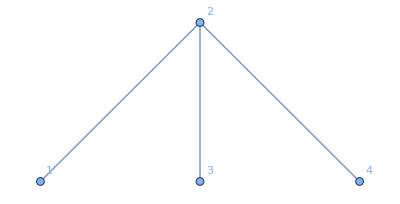
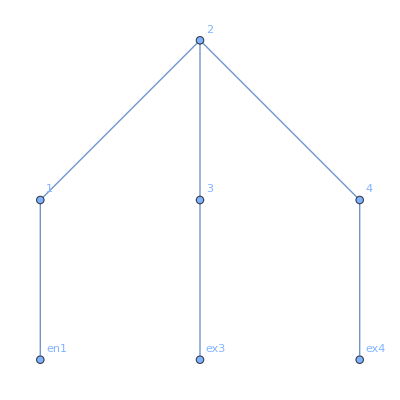
{0.074926,Missing[KeyAbsent,<|Vertices List→{1,2,3,4},Adjacency Matrix→{{0,1,0,0},{0,0,1,1},{0,0,0,0},{0,0,0,0}},Entrance Vertices and Flows→{{1,1}},Exit Vertices and Terminal Costs→{{3,0},{4,0}},Switching Costs→{{1,2,3,1},{1,2,4,2},{3,2,1,1},{3,2,4,1},{4,2,1,2},{4,2,3,1}},graph→-Graphics-,pairs→{{1,2},{2,3},{2,4},{2,1},{3,2},{4,2}},entryVertices→{1},auxEntryVertices→{en1},exitVertices→{3,4},auxExitVertices→{ex3,ex4},entryEdges→{en1<->1},exitEdges→{3<->ex3,4<->ex4},auxiliaryGraph→-Graphics-,auxEdgeList→{1<->2,1<->en1,2<->3,2<->4,3<->ex3,4<->ex4},edgeList→{1<->2,2<->3,2<->4},auxVerticesList→{1,2,3,4,en1,ex3,ex4},auxTriples→{{2,1,en1},{en1,1,2},{1,2,3},{1,2,4},{3,2,1},{3,2,4},{4,2,1},{4,2,3},{2,3,ex3},{ex3,3,2},{2,4,ex4},{ex4,4,2}},EntryDataAssociation→<|{en1,1}→1|>,ExitCosts→<|ex3→0,ex4→0|>,js→{j[en1,1],j[1,en1],j[ex3,3],j[ex4,4],j[3,ex3],j[4,ex4],j[1,2],j[2,3],j[2,4],j[2,1],j[3,2],j[4,2]},us→{u[en1,1],u[1,en1],u[ex3,3],u[ex4,4],u[3,ex3],u[4,ex4],u[1,2],u[2,3],u[2,4],u[2,1],u[3,2],u[4,2]},jts→{j[2,1,en1],j[en1,1,2],j[1,2,3],j[1,2,4],j[3,2,1],j[3,2,4],j[4,2,1],j[4,2,3],j[2,3,ex3],j[ex3,3,2],j[2,4,ex4],j[ex4,4,2]},SignedFlows→<|{en1,1}→-j[1,en1]+j[en1,1],{3,ex3}→j[3,ex3]-j[ex3,3],{4,ex4}→j[4,ex4]-j[ex4,4],{1,2}→j[1,2]-j[2,1],{2,3}→j[2,3]-j[3,2],{2,4}→j[2,4]-j[4,2]|>,SwitchingCosts→<|{2,1,en1}→0,{en1,1,2}→0,{1,2,3}→1,{1,2,4}→2,{3,2,1}→1,{3,2,4}→1,{4,2,1}→2,{4,2,3}→1,{2,3,ex3}→0,{ex3,3,2}→0,{2,4,ex4}→0,{ex4,4,2}→0|>,IneqJs→j[en1,1]≥0&&j[1,en1]≥0&&j[ex3,3]≥0&&j[ex4,4]≥0&&j[3,ex3]≥0&&j[4,ex4]≥0&&j[1,2]≥0&&j[2,3]≥0&&j[2,4]≥0&&j[2,1]≥0&&j[3,2]≥0&&j[4,2]≥0,IneqJts→j[2,1,en1]≥0&&j[en1,1,2]≥0&&j[1,2,3]≥0&&j[1,2,4]≥0&&j[3,2,1]≥0&&j[3,2,4]≥0&&j[4,2,1]≥0&&j[4,2,3]≥0&&j[2,3,ex3]≥0&&j[ex3,3,2]≥0&&j[2,4,ex4]≥0&&j[ex4,4,2]≥0,AltFlows→(j[en1,1]==0||j[1,en1]==0)&&(j[1,en1]==0||j[en1,1]==0)&&(j[ex3,3]==0||j[3,ex3]==0)&&(j[ex4,4]==0||j[4,ex4]==0)&&(j[3,ex3]==0||j[ex3,3]==0)&&(j[4,ex4]==0||j[ex4,4]==0)&&(j[1,2]==0||j[2,1]==0)&&(j[2,3]==0||j[3,2]==0)&&(j[2,4]==0||j[4,2]==0)&&(j[2,1]==0||j[1,2]==0)&&(j[3,2]==0||j[2,3]==0)&&(j[4,2]==0||j[2,4]==0),AltTransitionFlows→(j[2,1,en1]==0||j[en1,1,2]==0)&&(j[en1,1,2]==0||j[2,1,en1]==0)&&(j[1,2,3]==0||j[3,2,1]==0)&&(j[1,2,4]==0||j[4,2,1]==0)&&(j[3,2,1]==0||j[1,2,3]==0)&&(j[3,2,4]==0||j[4,2,3]==0)&&(j[4,2,1]==0||j[1,2,4]==0)&&(j[4,2,3]==0||j[3,2,4]==0)&&(j[2,3,ex3]==0||j[ex3,3,2]==0)&&(j[ex3,3,2]==0||j[2,3,ex3]==0)&&(j[2,4,ex4]==0||j[ex4,4,2]==0)&&(j[ex4,4,2]==0||j[2,4,ex4]==0),splittingPairs→{{en1,1},{ex3,3},{ex4,4},{1,2},{2,3},{2,4},{2,1},{3,2},{4,2}},EqBalanceSplittingFlows→j[en1,1]==j[en1,1,2]&&j[ex3,3]==j[ex3,3,2]&&j[ex4,4]==j[ex4,4,2]&&j[1,2]==j[1,2,3]+j[1,2,4]&&j[2,3]==j[2,3,ex3]&&j[2,4]==j[2,4,ex4]&&j[2,1]==j[2,1,en1]&&j[3,2]==j[3,2,1]+j[3,2,4]&&j[4,2]==j[4,2,1]+j[4,2,3],BalanceSplittingFlows→{j[en1,1]-j[en1,1,2],j[ex3,3]-j[ex3,3,2],j[ex4,4]-j[ex4,4,2],j[1,2]-j[1,2,3]-j[1,2,4],j[2,3]-j[2,3,ex3],j[2,4]-j[2,4,ex4],j[2,1]-j[2,1,en1],j[3,2]-j[3,2,1]-j[3,2,4],j[4,2]-j[4,2,1]-j[4,2,3]},NoDeadStarts→{{1,en1},{3,ex3},{4,ex4},{1,2},{2,3},{2,4},{2,1},{3,2},{4,2}},RuleBalanceGatheringFlows→<|j[1,en1]→j[2,1,en1],j[3,ex3]→j[2,3,ex3],j[4,ex4]→j[2,4,ex4],j[1,2]→j[en1,1,2],j[2,3]→j[1,2,3]+j[4,2,3],j[2,4]→j[1,2,4]+j[3,2,4],j[2,1]→j[3,2,1]+j[4,2,1],j[3,2]→j[ex3,3,2],j[4,2]→j[ex4,4,2]|>,BalanceGatheringFlows→{-j[1,en1]+j[2,1,en1],-j[3,ex3]+j[2,3,ex3],-j[4,ex4]+j[2,4,ex4],-j[1,2]+j[en1,1,2],-j[2,3]+j[1,2,3]+j[4,2,3],-j[2,4]+j[1,2,4]+j[3,2,4],-j[2,1]+j[3,2,1]+j[4,2,1],-j[3,2]+j[ex3,3,2],-j[4,2]+j[ex4,4,2]},EqBalanceGatheringFlows→j[1,en1]==j[2,1,en1]&&j[3,ex3]==j[2,3,ex3]&&j[4,ex4]==j[2,4,ex4]&&j[1,2]==j[en1,1,2]&&j[2,3]==j[1,2,3]+j[4,2,3]&&j[2,4]==j[1,2,4]+j[3,2,4]&&j[2,1]==j[3,2,1]+j[4,2,1]&&j[3,2]==j[ex3,3,2]&&j[4,2]==j[ex4,4,2],EqEntryIn→{j[en1,1]==1},RuleEntryOut→<|j[1,en1]→0|>,RuleEntryValues→<|u[1,en1]→u[en1,1]|>,RuleExitFlowsIn→<|j[ex3,3]→0,j[ex4,4]→0|>,RuleExitValues→<|u[ex3,3]→0,u[ex4,4]→0,u[3,ex3]→0,u[4,ex4]→0|>,EqValueAuxiliaryEdges→u[en1,1]==u[1,en1]&&u[3,ex3]==u[ex3,3]&&u[4,ex4]==u[ex4,4],IneqSwitchingByVertex→{u[2,1]≤u[en1,1]&&u[en1,1]≤u[2,1],u[1,2]≤1+u[3,2]&&u[1,2]≤2+u[4,2]&&u[3,2]≤1+u[1,2]&&u[3,2]≤1+u[4,2]&&u[4,2]≤2+u[1,2]&&u[4,2]≤1+u[3,2],u[2,3]≤u[ex3,3]&&u[ex3,3]≤u[2,3],u[2,4]≤u[ex4,4]&&u[ex4,4]≤u[2,4]},AltOptCond→(j[2,1,en1]==0||u[2,1]==u[en1,1])&&(j[en1,1,2]==0||u[en1,1]==u[2,1])&&(j[1,2,3]==0||u[1,2]==1+u[3,2])&&(j[1,2,4]==0||u[1,2]==2+u[4,2])&&(j[3,2,1]==0||u[3,2]==1+u[1,2])&&(j[3,2,4]==0||u[3,2]==1+u[4,2])&&(j[4,2,1]==0||u[4,2]==2+u[1,2])&&(j[4,2,3]==0||u[4,2]==1+u[3,2])&&(j[2,3,ex3]==0||u[2,3]==u[ex3,3])&&(j[ex3,3,2]==0||u[ex3,3]==u[2,3])&&(j[2,4,ex4]==0||u[2,4]==u[ex4,4])&&(j[ex4,4,2]==0||u[ex4,4]==u[2,4]),Nlhs→{j[1,2]-j[2,1]+u[1,2]-u[2,1],j[2,3]-j[3,2]+u[2,3]-u[3,2],j[2,4]-j[4,2]+u[2,4]-u[4,2]},Nrhs→{j[1,2]-j[2,1]-IntM[j[1,2]-j[2,1],{1,2}] Sign[j[1,2]-j[2,1]],j[2,3]-j[3,2]-IntM[j[2,3]-j[3,2],{2,3}] Sign[j[2,3]-j[3,2]],j[2,4]-j[4,2]-IntM[j[2,4]-j[4,2],{2,4}] Sign[j[2,4]-j[4,2]]},costpluscurrents→<|cpc1→j[1,2]-j[2,1]-IntM[j[1,2]-j[2,1],{1,2}] Sign[j[1,2]-j[2,1]],cpc2→j[2,3]-j[3,2]-IntM[j[2,3]-j[3,2],{2,3}] Sign[j[2,3]-j[3,2]],cpc3→j[2,4]-j[4,2]-IntM[j[2,4]-j[4,2],{2,4}] Sign[j[2,4]-j[4,2]]|>,EqGeneral→j[1,2]-j[2,1]+u[1,2]-u[2,1]==cpc1&&j[2,3]-j[3,2]+u[2,3]-u[3,2]==cpc2&&j[2,4]-j[4,2]+u[2,4]-u[4,2]==cpc3,InitRules→<|j[en1,1]→1,j[1,en1]→0,j[ex3,3]→0,j[ex4,4]→0,u[1,en1]→1-cpc1+u[1,2],j[3,ex3]→j[2,3,ex3],j[4,ex4]→1-j[2,3,ex3],j[1,2]→1,j[2,3]→j[2,3,ex3],j[2,4]→1-j[2,3,ex3],j[2,1]→0,j[3,2]→0,j[4,2]→0,u[ex3,3]→0,u[ex4,4]→0,u[3,ex3]→0,u[4,ex4]→0,j[1,2,4]→1-j[1,2,3],j[2,4,ex4]→1-j[2,3,ex3],j[3,2,1]→-j[1,2,3]+j[2,3,ex3],j[3,2,4]→j[1,2,3]-j[2,3,ex3],j[4,2,1]→j[1,2,3]-j[2,3,ex3],j[4,2,3]→-j[1,2,3]+j[2,3,ex3],j[en1,1,2]→1,j[ex3,3,2]→0,j[ex4,4,2]→0,u[2,3]→0,u[2,4]→0,u[en1,1]→1-cpc1+u[1,2],j[2,1,en1]→0,u[2,1]→1-cpc1+u[1,2],u[3,2]→-cpc2+j[2,3,ex3],u[4,2]→1-cpc3-j[2,3,ex3]|>,NewSystem→{True,j[1,2,3]≥0&&1-j[1,2,3]≥0&&-j[1,2,3]+j[2,3,ex3]≥0&&j[1,2,3]-j[2,3,ex3]≥0&&j[1,2,3]-j[2,3,ex3]≥0&&-j[1,2,3]+j[2,3,ex3]≥0&&j[2,3,ex3]≥0&&1-j[2,3,ex3]≥0&&j[2,3,ex3]≥0&&1-j[2,3,ex3]≥0&&j[2,3,ex3]≥0&&1-j[2,3,ex3]≥0&&-1≤cpc2-j[2,3,ex3]+u[1,2]≤1&&-2≤-1+cpc3+j[2,3,ex3]+u[1,2]≤2&&-1≤-1-cpc2+cpc3+2 j[2,3,ex3]≤1,(j[1,2,3]==0||-j[1,2,3]+j[2,3,ex3]==0)&&(1-j[1,2,3]==0||j[1,2,3]-j[2,3,ex3]==0)&&(-j[1,2,3]+j[2,3,ex3]==0||j[1,2,3]==0)&&(j[1,2,3]-j[2,3,ex3]==0||-j[1,2,3]+j[2,3,ex3]==0)&&(j[1,2,3]-j[2,3,ex3]==0||1-j[1,2,3]==0)&&(-j[1,2,3]+j[2,3,ex3]==0||j[1,2,3]-j[2,3,ex3]==0)&&(j[1,2,3]==0||u[1,2]==1-cpc2+j[2,3,ex3])&&(1-j[1,2,3]==0||u[1,2]==3-cpc3-j[2,3,ex3])&&(-j[1,2,3]+j[2,3,ex3]==0||-cpc2+j[2,3,ex3]==1+u[1,2])&&(j[1,2,3]-j[2,3,ex3]==0||-cpc2+j[2,3,ex3]==2-cpc3-j[2,3,ex3])&&(j[1,2,3]-j[2,3,ex3]==0||1-cpc3-j[2,3,ex3]==2+u[1,2])&&(-j[1,2,3]+j[2,3,ex3]==0||1-cpc3-j[2,3,ex3]==1-cpc2+j[2,3,ex3])},AssoCritical→<|u[en1,1]→3,u[1,en1]→3,u[ex3,3]→0,u[ex4,4]→0,u[3,ex3]→0,u[4,ex4]→0,u[1,2]→2,u[2,3]→0,u[2,4]→0,u[2,1]→3,u[3,2]→1,u[4,2]→0,j[en1,1]→1,j[1,en1]→0,j[ex3,3]→0,j[ex4,4]→0,j[3,ex3]→1,j[4,ex4]→0,j[1,2]→1,j[2,3]→1,j[2,4]→0,j[2,1]→0,j[3,2]→0,j[4,2]→0,j[2,1,en1]→0,j[en1,1,2]→1,j[1,2,3]→1,j[1,2,4]→0,j[3,2,1]→0,j[3,2,4]→0,j[4,2,1]→0,j[4,2,3]→0,j[2,3,ex3]→1,j[ex3,3,2]→0,j[2,4,ex4]→0,j[ex4,4,2]→0|>|>]}

```mathematica
NonLinear[d2e][cjs]//AbsoluteTiming
```

```mathematica
(cjs=CriticalCongestionSolver[d2e];)//AbsoluteTiming
```

{0.008213,Null}